## Exact solution for two-particle system

The Schrodinger Equation for two particles is

	(-∂^2/(∂s_1^2)-∂^2/(∂s_2^2)+s_1^2+s_2^2-1/2 β(s_1-s_2)^2)ψ[s_1,s_2]=Eψ[s_1,s_2]
The wavefunction solution to this equation is
	ψ(x_1,x_2)=(x_1-x_2)Exp[-1/2(γ(x_1^2+x_2^2)+α x_1 x_2)]
with
	γ=1/2(1+√(1-β))	and	α=1-√(1-β)		with	E=1+3 √(1-β)
Note that γ+1/2 α=1 → α=2(1-γ).  This is not a general result (for N ≠ 2).  Note also that 1/2 < γ ≤ 1

### Basic Definitions

Use the result that α=2(1-γ) to eliminate α in the expression for the wavefunction

```mathematica
ψ[x1_,x2_]=(x1-x2)Exp[-1/2(γ(x1^2+x2^2)+α x1 x2)]/.{α->2(1-γ)}//FullSimplify
```

ⅇ^(-x1 x2-1/2 (x1-x2)^2 γ) (x1-x2)

```mathematica
γExact=1/2(1+√(1-β));
αExact=1-√(1-β);ψExact[x1_,x2_]=ψ[x1,x2]/.{γ->γExact}//FullSimplify
```

ⅇ^(-x1 x2-1/4 (x1-x2)^2 (1+√(1-β))) (x1-x2)

### Check that this is indeed the solution to the Schrodinger equation:

Evaluate Ĥ ψ:

```mathematica
LHS=Simplify[(-D[ψExact[x1,x2], x1,x1])+(-D[ψExact[x1,x2], x2,x2])+(x1^2+x2^2)ψExact[x1,x2]-1/2 β(x1-x2)^2 ψExact[x1,x2],Assumptions->β<1]
```

ⅇ^(-x1 x2-1/4 (x1-x2)^2 (1+√(1-β))) (x1-x2) (1+3 √(1-β))

This is equal to a contant times ψ.  Divide by ψ to show this.

```mathematica
eExact=FullSimplify[LHS/ψExact[x1,x2],Assumptions->β<1]
```

1+3 √(1-β)

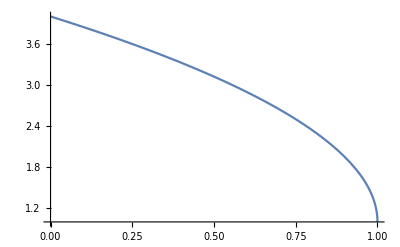

```mathematica
Plot[eExact,{β,0,1}]
```

### Determine density and kinetic energy density for arbitrary γ

Integrate to find the normalization constant.  This integral now is evaluated relatively quickly, but evaluation is “turned off” by using :=.  Also, the result is a bit ugly, so we will not bother to normalize the wavefunction.

```mathematica
ans:=Integrate[ψ[x1,x2]^2,{x1,-∞,∞},{x2,-∞,∞},Assumptions->{γ>1/2,γ≤ 1}]
```

```mathematica
normConst=(√((-1+2 γ)^(3/2)))/(√π);
```

Check that this works (again, this takes some time, so evaluation is turned off)

```mathematica
ans:=Integrate[normConst^2 ψ[x1,x2]^2,{x1,-∞,∞},{x2,-∞,∞},Assumptions->{γ>1/2,γ≤ 1}]
```

Find the one- and two-particle density matrices

```mathematica
ρ12[x1_,x2_]=ψ[x1,x2]^2
```

ⅇ^(-2 x1 x2-(x1-x2)^2 γ) (x1-x2)^2

```mathematica
ρ[x_]=Integrate[ρ12[x,x2],{x2,-∞,∞},Assumptions->{γ>1/2,γ≤ 1}]//FullSimplify
```

(ⅇ^((x^2 (1-2 γ))/γ) √π (2 x^2+γ))/(2 γ^(5/2))

Find the one- and two-particle kinetic energy expressions.  Note that the “a” versions use the (∂_x1 ψ[x1,x2])^2 expressions and the “b” version use  ψ[x1,x2]∂_(x1,x1) ψ[x1,x2].  the “a” version ensures k[x]≥0.  Both give the same result for the total kinetic energy

```mathematica
k12a[x1_,x2_]=(D[ψ[x1,x2], x1])^2+(D[ψ[x1,x2], x2])^2//FullSimplify
```

ⅇ^(-2 x1 x2-(x1-x2)^2 γ) (2+(x1-x2)^2 (2+x1^2+x2^2-2 (2+(x1-x2)^2) γ+2 (x1-x2)^2 γ^2))

```mathematica
k1a[x_]=Integrate[k12a[x,x2],{x2,-∞,∞},Assumptions->{γ>1/2,γ≤ 1}]//FullSimplify
```

1/(4 γ^(9/2))ⅇ^((x^2 (1-2 γ))/γ) √π (4 x^4 (1-2 γ)^2+γ^2 (3-2 γ+6 γ^2)+4 x^2 γ (3+γ (-7+3 γ)))

This looks a bit ugly, but it is just equal to (a +b x^2+c x^4)e^(-d x^2)

```mathematica
k12b[x1_,x2_]=(-ψ[x1,x2]D[ψ[x1,x2], x1,x1])+(-ψ[x1,x2]D[ψ[x1,x2], x2,x2])//FullSimplify
```

ⅇ^(-2 x1 x2-(x1-x2)^2 γ) (x1-x2)^2 (-2-x1^2-x2^2+2 (3+(x1-x2)^2) γ-2 (x1-x2)^2 γ^2)

```mathematica
k1b[x_]=Integrate[k12b[x,x2],{x2,-∞,∞},Assumptions->{γ>1/2,γ≤ 1}]//FullSimplify
```

(ⅇ^((x^2 (1-2 γ))/γ) √π (-4 x^4 (1-2 γ)^2-4 x^2 γ (3+(-7+γ) γ)+γ^2 (-3+2 γ+6 γ^2)))/(4 γ^(9/2))

Show that both versions give the same total kinetic energy

```mathematica
kTota=Integrate[k1a[x],{x,-∞,∞},Assumptions->{γ>1/2,γ≤ 1}]//FullSimplify
```

(π (-1+3 γ))/(-1+2 γ)^(3/2)

```mathematica
kTotb=Integrate[k1b[x],{x,-∞,∞},Assumptions->{γ>1/2,γ≤ 1}]//FullSimplify
```

(π (-1+3 γ))/(-1+2 γ)^(3/2)

### Divide out prefactor and Gaussian to write kinetic energy, density and derivatives as polynomials

```mathematica
ρ[x]
```

(ⅇ^((x^2 (1-2 γ))/γ) √π (2 x^2+γ))/(2 γ^(5/2))

```mathematica
preFact=ρ[x]/(2 x^2+γ)//FullSimplify
```

(ⅇ^((x^2 (1-2 γ))/γ) √π)/(2 γ^(5/2))

```mathematica
ρ0=ρ[x]/preFact//FullSimplify
```

2 x^2+γ

```mathematica
kina=k1a[x]/preFact
```

1/(2 γ^2)(4 x^4 (1-2 γ)^2+γ^2 (3-2 γ+6 γ^2)+4 x^2 γ (3+γ (-7+3 γ)))

```mathematica
ρP=Collect[(D[ρ[x], x])/preFact//FullSimplify,x]
```

4 x^3 (-2+1/γ)+x (6-4 γ)

```mathematica
ρPP=Collect[(D[ρ[x], x,x])/preFact//FullSimplify,x]
```

2 (3-2 γ)+(8 x^4 (1-2 γ)^2)/γ^2+(8 x^2 (-3+γ) (-1+2 γ))/γ

```mathematica
ρPPP=Collect[(D[ρ[x], x,x,x])/preFact//FullSimplify,x]
```

-(16 x^5 (1-2 γ)^2 (-1+2 γ))/γ^3-(12 x (5-2 γ) (-1+2 γ))/γ-(16 x^3 (-5+γ) (-1+2 γ)^2)/γ^2

```mathematica
ρPPPP=Collect[(D[ρ[x], x,x,x,x])/preFact//FullSimplify,x]
```

(16 x^4 (1-2 γ)^2 (-15+2 γ) (-1+2 γ))/γ^3+(12 (-5+2 γ) (-1+2 γ))/γ+(32 x^6 (-1+2 γ)^4)/γ^4-(24 x^2 (-1+2 γ) (15-34 γ+8 γ^2))/γ^2

Consider these when γ=1.  This corresponds to β=0 so they should give the same results we found earlier i

```mathematica
Collect[{kina,ρ0,ρP,ρPP,ρPPP,ρPPPP}/.γ->1//FullSimplify,x]//TableForm
```

7/2-2 x^2+2 x^4
1+2 x^2
2 x-4 x^3
2-16 x^2+8 x^4
-36 x+64 x^3-16 x^5
-36+264 x^2-208 x^4+32 x^6

We had found a combination of rho and its derivatives that generate a fourth order polynomial:

```mathematica
fρ=1/4(ρPP^2-ρP ρPPP)/ρ0/.γ->1//FullSimplify
```

1+4 x^4

Which then allowed us to write the kinetic energy density as a function of ρ,  ρPP and fρ

```mathematica
3ρ0+1/2 ρPP-1/2 fρ/.γ->1//FullSimplify
```

7/2-2 x^2+2 x^4

Can we do the same thing when γ ≠ 1(i.e. β ≠ 0)?  Consider the density and derivatives when γ=3/4.

```mathematica
Collect[{kina,ρ0,ρP,ρPP,ρPPP,ρPPPP}/.γ->3/4//FullSimplify,x]//TableForm
```

39/16-(3 x^2)/2+(8 x^4)/9
3/4+2 x^2
3 x-(8 x^3)/3
3-12 x^2+(32 x^4)/9
-28 x+(272 x^3)/9-(128 x^5)/27
-28+128 x^2-64 x^4+(512 x^6)/81

These are just polynomials like we had for the non-interacting case, so we can probably find combinations of rho and its derivatives that generate the kinetic energy density.

### Determine a combination of the density and derivatives that gives a 4th order equation for γ=3/4.

```mathematica
kin=Collect[kina/.γ->3/4//FullSimplify,x]
rho=Collect[ρ0/.γ->3/4//FullSimplify,x]
rp=Collect[ρP/.γ->3/4//FullSimplify,x]
rpp=Collect[ρPP/.γ->3/4//FullSimplify,x]
rppp=Collect[ρPPP/.γ->3/4//FullSimplify,x]
rpppp=Collect[ρPPPP/.γ->3/4//FullSimplify,x]
```

39/16-(3 x^2)/2+(8 x^4)/9

3/4+2 x^2

3 x-(8 x^3)/3

3-12 x^2+(32 x^4)/9

-28 x+(272 x^3)/9-(128 x^5)/27

-28+128 x^2-64 x^4+(512 x^6)/81

#### First consider only terms up to rppp. We find (rp^2+3/2(rpp^2-rp rppp))/rho=18-12 x^2+(32 x^4)/3 But this turns out to be a linear combination of rho and rpp. Who would have known?

Can we find a rp^2+b rpp^2+c rppp +d rp rpp+e rp rppp +f rpp rppp=rho f[x] where f[x] is a simple polynomial?

```mathematica
poly=Collect[a rp^2+b rpp^2+c rppp^2+d rp rpp+e rp rppp+f rpp rppp,x]
```

```mathematica
ans=Collect[FullSimplify[a rp^2+b rpp^2+c rppp^2+d rp rpp+e rp rppp+f rpp rppp-rho(g+h x+i x^2+j x^3+k x^4+n x^5+q x^6+r x^7+s x^8),Assumptions->{a>0,b>0,c>0,d>0,e>0,f>0,g>0,h>0,i>0,j>0,k>0,n>0,q>0,r>0,s>0}],x]
```

9 b-(3 g)/4+(9 d-84 f-(3 h)/4) x+(9 a-72 b+784 c-84 e-2 g-(3 i)/4) x^2+(-44 d+(1280 f)/3-2 h-(3 j)/4) x^3+(-16 a+(496 b)/3-(15232 c)/9+(496 e)/3-2 i-(3 k)/4) x^4+((128 d)/3-(4288 f)/9-2 j-(3 n)/4) x^5+((64 a)/9-(256 b)/3+(95488 c)/81-(2560 e)/27-2 k-(3 q)/4) x^6+(-(256 d)/27+(13312 f)/81-2 n-(3 r)/4) x^7+((1024 b)/81-(69632 c)/243+(1024 e)/81-2 q-(3 s)/4) x^8+(-(4096 f)/243-2 r) x^9+((16384 c)/729-2 s) x^10

```mathematica
Collect[FullSimplify[ans/.{s->c 8192/729,r->-f 2048/243,g->12b}],x]
```

1/972 (8748 d-81648 f-729 h) x-1/4 (-36 a+384 b-3136 c+336 e+3 i) x^2-1/12 (528 d-5120 f+24 h+9 j) x^3-1/36 (64 (9 a-93 b+952 c-93 e)+72 i+27 k) x^4+1/36 (1536 d-17152 f-9 (8 j+3 n)) x^5+1/324 (256 (9 a-4 (27 b-373 c+30 e))-648 k-243 q) x^6-2/27 (128 (d-18 f)+27 n) x^7+2/243 (512 (3 b-70 c+3 e)-243 q) x^8

```mathematica
Collect[FullSimplify[ans/.{s->c 8192/729,r->-f 2048/243,g->12b}/.{q->512(3b-70c+3e)/243}/.{n->-128(d-18f)/27}],x]
```

1/108 (972 d-9072 f-81 h) x-1/4 (-36 a+384 b-3136 c+336 e+3 i) x^2-1/12 (528 d-5120 f+24 h+9 j) x^3-1/36 (64 (9 a-93 b+952 c-93 e)+72 i+27 k) x^4+2/9 (208 d-2432 f-9 j) x^5+2/27 (32 (3 a-38 b+544 c-42 e)-27 k) x^6

```mathematica
Collect[FullSimplify[ans/.{s->c 8192/729,r->-f 2048/243,g->12b}/.{q->512(3b-70c+3e)/243}/.{n->-128(d-18f)/27}/.{k->32(3 a-38 b+544 c-42 e)/27,j->(208d-2432f)/9}],x]
```

1/36 (324 d-3024 f-27 h) x-1/4 (-36 a+384 b-3136 c+336 e+3 i) x^2-2/3 (92 d-944 f+3 h) x^3-2/9 (84 a-896 b+9792 c-912 e+9 i) x^4

```mathematica
Collect[FullSimplify[ans/.{s->c 8192/729,r->-f 2048/243,g->12b}/.{q->512(3b-70c+3e)/243}/.{n->-128(d-18f)/27}/.{k->32(3 a-38 b+544 c-42 e)/27,j->(208d-2432f)/9}/.{i->-(84a-896b+9792c-912e)/9,h->-(92d-944f)/3}],x]
```

16/3 (6 d-60 f) x+16/3 (3 a-32 b+300 c-30 e) x^2

```mathematica
Collect[FullSimplify[ans/.{s->c 8192/729,r->-f 2048/243,g->12b}/.{q->512(3b-70c+3e)/243}/.{n->-128(d-18f)/27}/.{k->32(3 a-38 b+544 c-42 e)/27,j->(208d-2432f)/9}/.{i->-(84a-896b+9792c-912e)/9,h->-(92d-944f)/3}/.{f->d/10,e->(3a-32b+300c)/30}],x]
```

0

Now put all these substitutions into the product expression divided by rho.  It should be a simple polynomial

```mathematica
ans=Collect[FullSimplify[a rp^2+b rpp^2+c rppp^2+d rp rpp+e rp rppp+f rpp rppp,Assumptions->{a>0,b>0,c>0,d>0,e>0,f>0,g>0,h>0,i>0,j>0,k>0,n>0,q>0,r>0,s>0}],x]
```

9 b+1/729 (6561 d-61236 f) x+1/729 (6561 a-52488 b+571536 c-61236 e) x^2+1/729 (-32076 d+311040 f) x^3+1/729 (-11664 a+120528 b-1233792 c+120528 e) x^4+1/729 (31104 d-347328 f) x^5+1/729 (5184 a-62208 b+859392 c-69120 e) x^6+1/729 (-6912 d+119808 f) x^7+1/729 (9216 b-208896 c+9216 e) x^8-(4096 f x^9)/243+(16384 c x^10)/729

```mathematica
ans=Collect[FullSimplify[(ans/rho)/.{s->c 8192/729,r->-f 2048/243,g->12b}/.{q->512(3b-70c+3e)/243}/.{n->-128(d-18f)/27}/.{k->32(3 a-38 b+544 c-42 e)/27,j->(208d-2432f)/9}/.{i->-(84a-896b+9792c-912e)/9,h->-(92d-944f)/3}/.{f->d/10,e->(3a-32b+300c)/30}],x]
```

12 b+(4 d x)/5+(4 (729 a-7776 b-68040 c) x^2)/3645-(176 d x^3)/45+(4 (-1296 a+7344 b+133920 c) x^4)/3645+(512 d x^5)/135+(4 (576 a-384 b-76800 c) x^6)/3645-(1024 d x^7)/1215+(8192 c x^8)/729

Can we eliminate the higher powers of x (and the odd powers) without making the entire expression disappear?

```mathematica
Collect[FullSimplify[ans/.{c->0,d->0}],x]
```

12 b+(4 (243 a-2592 b) x^2)/1215+(4 (-432 a+2448 b) x^4)/1215+(4 (192 a-128 b) x^6)/1215

```mathematica
Collect[FullSimplify[ans/.{c->0,d->0}/.b->a 192/128],x]
```

18 a-12 a x^2+(32 a x^4)/3

Determine the values of the coefficients that accomplish this.

```mathematica
{a,b,c,d,e,f}/.{s->c 8192/729,r->-f 2048/243,g->12b}/.{q->512(3b-70c+3e)/243}/.{n->-128(d-18f)/27}/.{k->32(3 a-38 b+544 c-42 e)/27,j->(208d-2432f)/9}/.{i->-(84a-896b+9792c-912e)/9,h->-(92d-944f)/3}/.{f->d/10,e->(3a-32b+300c)/30}/.{c->0,d->0}/.b->a 192/128
```

{a,(3 a)/2,0,0,-(3 a)/2,0}

Recall that the polynomial is given by
	a rp^2+b rpp^2+c rppp +d rp rpp+e rp rppp +f rpp rppp

```mathematica
fp=(rp^2+3/2(rpp^2-rp rppp))/rho//FullSimplify
```

18-12 x^2+(32 x^4)/3

```mathematica
{rho,rpp,fp}
```

{3/4+2 x^2,3-12 x^2+(32 x^4)/9,18-12 x^2+(32 x^4)/3}

Turns out that fp is a linear combination of rho and rpp - bummer!

```mathematica
ans=Collect[a rho +b rpp- fp,x]
```

-18+(3 a)/4+3 b+(12+2 a-12 b) x^2+(-32/3+(32 b)/9) x^4

```mathematica
ans/.b->3
```

-9+(3 a)/4+(-24+2 a) x^2

```mathematica
ans/.{b->3,a->12}
```

0

Is it possible the kinetic energy can be written in terms of rho and rpp alone?

```mathematica
ans=Collect[a rho +b rpp- kin,x]
```

-39/16+(3 a)/4+3 b+(3/2+2 a-12 b) x^2+(-8/9+(32 b)/9) x^4

```mathematica
ans/.b->1/4
```

-27/16+(3 a)/4+(-3/2+2 a) x^2

```mathematica
ans/.{b->1/4,a->3/4}
```

-9/8

```mathematica
fp=(rp^2+3/2(rpp^2-rp rppp))/rho//FullSimplify
```

#### Consider all terms including rpppp.

```mathematica
poly=Collect[a rp^2+b rpp^2+c rppp^2+d rpppp^2+e rp rpp+f rp rppp+g rp rpppp+h rpp rppp + i rpp rpppp+j rppp rpppp,x]
```

9 b+784 d-84 i+(9 e-84 g-84 h+784 j) x+(9 a-72 b+784 c-7168 d-84 f+720 i) x^2+(-44 e+(1376 g)/3+(1280 h)/3-(39872 j)/9) x^3+(-16 a+(496 b)/3-(15232 c)/9+19968 d+(496 f)/3-(16448 i)/9) x^4+((128 e)/3-(1600 g)/3-(4288 h)/9+(156416 j)/27) x^5+((64 a)/9-(256 b)/3+(95488 c)/81-(1355776 d)/81-(2560 f)/27+(33536 i)/27) x^6+(-(256 e)/27+(5120 g)/27+(13312 h)/81-(220160 j)/81) x^7+((1024 b)/81-(69632 c)/243+(462848 d)/81+(1024 f)/81-(8192 i)/27) x^8+(-(4096 g)/243-(4096 h)/243+(360448 j)/729) x^9+((16384 c)/729-(65536 d)/81+(16384 i)/729) x^10-(65536 j x^11)/2187+(262144 d x^12)/6561

```mathematica
ans=Collect[FullSimplify[poly-rho(k+m x+n x^2+o x^3+p x^4+q x^5+r x^6+s x^7+t x^8+u x^9+v x^10)],x]
```

9 b+784 d-84 i-(3 k)/4+(9 e-84 (g+h)+784 j-(3 m)/4) x+(9 a-72 b+784 c-7168 d-84 f+720 i-2 k-(3 n)/4) x^2+(-4/9 (99 e-1032 g-960 h+9968 j)-2 m-(3 o)/4) x^3+(-16/9 (9 a-93 b+952 c-11232 d-93 f+1028 i)-2 n-(3 p)/4) x^4+(64/27 (18 e-225 g-201 h+2444 j)-2 o-(3 q)/4) x^5+(64/81 (9 a-4 (27 b-373 c+5296 d+30 f-393 i))-2 p-(3 r)/4) x^6+(-256/81 (3 e-60 g-52 h+860 j)-2 q-(3 s)/4) x^7+(1024/243 (3 b-68 c+3 (452 d+f-24 i))-2 r-(3 t)/4) x^8+(-4096/729 (3 (g+h)-88 j)-2 s-(3 u)/4) x^9+(16384/729 (c-36 d+i)-2 t-(3 v)/4) x^10+(-(65536 j)/2187-2 u) x^11+((262144 d)/6561-2 v) x^12

```mathematica
ans=Collect[FullSimplify[poly-rho(k+m x+n x^2+o x^3+p x^4+q x^5+r x^6+s x^7+t x^8+u x^9+v x^10),Assumptions->{a>0,b>0,c>0,d>0,e>0,f>0,g>0,h>0,i>0,j>0,k>0,n>0,q>0,r>0,s>0,t>0,u>0,v>0}],x]
```

9 b+784 d-84 i-(3 k)/4+(9 e-84 (g+h)+784 j-(3 m)/4) x+(9 a-72 b+784 c-7168 d-84 f+720 i-2 k-(3 n)/4) x^2+(-4/9 (99 e-1032 g-960 h+9968 j)-2 m-(3 o)/4) x^3+(-16/9 (9 a-93 b+952 c-11232 d-93 f+1028 i)-2 n-(3 p)/4) x^4+(64/27 (18 e-225 g-201 h+2444 j)-2 o-(3 q)/4) x^5+(64/81 (9 a-4 (27 b-373 c+5296 d+30 f-393 i))-2 p-(3 r)/4) x^6+(-256/81 (3 e-60 g-52 h+860 j)-2 q-(3 s)/4) x^7+(1024/243 (3 b-68 c+3 (452 d+f-24 i))-2 r-(3 t)/4) x^8+(-4096/729 (3 (g+h)-88 j)-2 s-(3 u)/4) x^9+(16384/729 (c-36 d+i)-2 t-(3 v)/4) x^10+(-(65536 j)/2187-2 u) x^11+((262144 d)/6561-2 v) x^12

```mathematica
Collect[FullSimplify[ans/.{v->d 262144/(2*6561),u->-j 65536/(2*2187)}],x]
```

9 b+784 d-84 i-(3 k)/4+(9 e-84 (g+h)+784 j-(3 m)/4) x+(9 a-72 b+784 c-7168 d-84 f+720 i-2 k-(3 n)/4) x^2+(-44 e+32/9 (129 g+120 h-1246 j)-2 m-(3 o)/4) x^3+(-16 a+16/9 (93 b-952 c+11232 d+93 f-1028 i)-2 n-(3 p)/4) x^4+(64/27 (18 e-225 g-201 h+2444 j)-2 o-(3 q)/4) x^5+(64/81 (9 a-4 (27 b-373 c+5296 d+30 f-393 i))-2 p-(3 r)/4) x^6+(-256/81 (3 e-60 g-52 h+860 j)-2 q-(3 s)/4) x^7+(1024/243 (3 b-68 c+3 (452 d+f-24 i))-2 r-(3 t)/4) x^8-2/243 (2048 (g+h-30 j)+243 s) x^9+(2 (8192 (3 c-110 d+3 i)-2187 t) x^10)/2187

```mathematica
Collect[FullSimplify[ans/.{v->d 262144/(2*6561),u->-j 65536/(2*2187)}/.{t->8192 (3 c-110 d+3 i)/2187,s->-2048 (g+h-30 j)/243}],x]
```

9 b+784 d-84 i-(3 k)/4+(9 e-84 (g+h)+784 j-(3 m)/4) x+(9 a-72 b+784 c-7168 d-84 f+720 i-2 k-(3 n)/4) x^2+(-44 e+32/9 (129 g+120 h-1246 j)-2 m-(3 o)/4) x^3+(-16 a+16/9 (93 b-952 c+11232 d+93 f-1028 i)-2 n-(3 p)/4) x^4+(64/27 (18 e-225 g-201 h+2444 j)-2 o-(3 q)/4) x^5+(64/81 (9 a-4 (27 b-373 c+5296 d+30 f-393 i))-2 p-(3 r)/4) x^6-2/81 (128 (3 e-62 g-54 h+920 j)+81 q) x^7+2/729 (512 (9 b-210 c+4288 d+9 f-222 i)-729 r) x^8

```mathematica
Collect[FullSimplify[ans/.{v->d 262144/(2*6561),u->-j 65536/(2*2187)}/.{t->8192 (3 c-110 d+3 i)/2187,s->-2048 (g+h-30 j)/243}/.{r->512 (9 b-210 c+4288 d+9 f-222 i)/729,q->-128 (3 e-62 g-54 h+920 j)/81}],x]
```

1/4 (36 b+3136 d-3 (112 i+k))+1/4 (36 e-336 (g+h)+3136 j-3 m) x-1/4 (-36 a+8 (36 b-392 c+3584 d+42 f-360 i+k)+3 n) x^2-1/36 (8 (198 e-2064 g-1920 h+19936 j+9 m)+27 o) x^3-1/36 (64 (9 a-93 b+952 c-11232 d-93 f+1028 i)+72 n+27 p) x^4+2/27 (624 e-128 (64 g+57 h-726 j)-27 o) x^5+2/243 (32 (27 a-342 b+4896 c-72128 d-378 f+5160 i)-243 p) x^6

```mathematica
Collect[FullSimplify[ans/.{v->d 262144/(2*6561),u->-j 65536/(2*2187)}/.{t->8192 (3 c-110 d+3 i)/2187,s->-2048 (g+h-30 j)/243}/.{r->512 (9 b-210 c+4288 d+9 f-222 i)/729,q->-128 (3 e-62 g-54 h+920 j)/81}/.{p->32 (27 a-342 b+4896 c-72128 d-378 f+5160 i)/243,o->(624 e-128 (64 g+57 h-726 j))/27}],x]
```

1/4 (36 b+3136 d-3 (112 i+k))+1/4 (36 e-336 (g+h)+3136 j-3 m) x-1/4 (-36 a+8 (36 b-392 c+3584 d+42 f-360 i+k)+3 n) x^2-2/9 (4 (69 e-772 g-708 h+7888 j)+9 m) x^3-2/81 (756 a-16 (504 b-5508 c+68576 d+513 f-5916 i)+81 n) x^4

```mathematica
Collect[FullSimplify[ans/.{v->d 262144/(2*6561),u->-j 65536/(2*2187)}/.{t->8192 (3 c-110 d+3 i)/2187,s->-2048 (g+h-30 j)/243}/.{r->512 (9 b-210 c+4288 d+9 f-222 i)/729,q->-128 (3 e-62 g-54 h+920 j)/81}/.{p->32 (27 a-342 b+4896 c-72128 d-378 f+5160 i)/243,o->(624 e-128 (64 g+57 h-726 j))/27}/.{n->-(756 a-16 (504 b-5508 c+68576 d+513 f-5916 i))/81,m->-4 (69 e-772 g-708 h+7888 j)/9}],x]
```

9 b+784 d-84 i-(3 k)/4+(32 e-(1024 g)/3-320 h+(10240 j)/3) x+(16 a-2/27 (4 (495 b-5400 c+58480 d+540 f-5388 i)+27 k)) x^2

```mathematica
Collect[FullSimplify[ans/.{v->d 262144/(2*6561),u->-j 65536/(2*2187)}/.{t->8192 (3 c-110 d+3 i)/2187,s->-2048 (g+h-30 j)/243}/.{r->512 (9 b-210 c+4288 d+9 f-222 i)/729,q->-128 (3 e-62 g-54 h+920 j)/81}/.{p->32 (27 a-342 b+4896 c-72128 d-378 f+5160 i)/243,o->(624 e-128 (64 g+57 h-726 j))/27}/.{n->-(756 a-16 (504 b-5508 c+68576 d+513 f-5916 i))/81,m->-4 (69 e-772 g-708 h+7888 j)/9}/.{k->(9 b+784 d-84 i)4/3}],x]
```

16/27 (54 e-576 g-540 h+5760 j) x+16/27 (27 a-288 b+2700 c-32768 d-270 f+3072 i) x^2

```mathematica
Collect[FullSimplify[ans/.{v->d 262144/(2*6561),u->-j 65536/(2*2187)}/.{t->8192 (3 c-110 d+3 i)/2187,s->-2048 (g+h-30 j)/243}/.{r->512 (9 b-210 c+4288 d+9 f-222 i)/729,q->-128 (3 e-62 g-54 h+920 j)/81}/.{p->32 (27 a-342 b+4896 c-72128 d-378 f+5160 i)/243,o->(624 e-128 (64 g+57 h-726 j))/27}/.{n->-(756 a-16 (504 b-5508 c+68576 d+513 f-5916 i))/81,m->-4 (69 e-772 g-708 h+7888 j)/9}/.{k->(9 b+784 d-84 i)4/3}/.{i->-(27 a-288 b+2700 c-32768 d-270 f)/3072,j->-(54 e-576 g-540 h)/5760}],x]
```

0

Now put all these substitutions into the product expression divided by rho.  It should be a simple polynomial

```mathematica
ans=Collect[FullSimplify[(poly/rho)/.{v->d 262144/(2*6561),u->-j 65536/(2*2187)}/.{t->8192 (3 c-110 d+3 i)/2187,s->-2048 (g+h-30 j)/243}/.{r->512 (9 b-210 c+4288 d+9 f-222 i)/729,q->-128 (3 e-62 g-54 h+920 j)/81}/.{p->32 (27 a-342 b+4896 c-72128 d-378 f+5160 i)/243,o->(624 e-128 (64 g+57 h-726 j))/27}/.{n->-(756 a-16 (504 b-5508 c+68576 d+513 f-5916 i))/81,m->-4 (69 e-772 g-708 h+7888 j)/9}/.{k->(9 b+784 d-84 i)4/3}/.{i->-(27 a-288 b+2700 c-32768 d-270 f)/3072,j->-(54 e-576 g-540 h)/5760}],x]
```

1/192 (189 a+288 b+18900 c-28672 d-1890 f)+1/15 (33 e-14 (8 g+15 h)) x+1/144 (135 a-2 (720 b+4386 c-77824 d+99 f)) x^2+4/135 (-309 e+1376 g+1770 h) x^3+1/324 (-783 a+6048 b+15396 c-729088 d+3222 f) x^4+16/27 (15 e-80 g-86 h) x^5+1/243 (333 a-2016 b-2540 c+327680 d-1794 f) x^6-64/243 (9 e-64 g-58 h) x^7+8/729 (-9 a+96 b+124 c-26624 d+90 f) x^8+(512 (3 e-32 g-30 h) x^9)/10935+(131072 d x^10)/6561

Can we eliminate the higher powers of x (and the odd powers) without making the entire expression disappear?

```mathematica
Collect[FullSimplify[ans/.{d->0,h->(3 e-32 g)/30}],x]
```

3/64 (21 a+32 b+2100 c-210 f)+4/15 (3 e+28 g) x+1/48 (45 a-480 b-2924 c-66 f) x^2-16/135 (33 e+128 g) x^3+1/108 (-261 a+2016 b+5132 c+1074 f) x^4+256/405 (6 e+11 g) x^5+1/243 (333 a-2 (1008 b+1270 c+897 f)) x^6-(1024 (3 e-2 g) x^7)/3645+8/729 (-9 a+96 b+124 c+90 f) x^8

```mathematica
Collect[FullSimplify[ans/.{d->0,h->(3 e-32 g)/30}/.{f->-(-9 a+96 b+124 c)/90,g->3e/2}],x]
```

(4 (10935 b+102060 c))/3645+12 e x+(4 (729 a-7776 b-53784 c) x^2)/3645-(80 e x^3)/3+(4 (-1296 a+7344 b+30816 c) x^4)/3645+(128 e x^5)/9+(4 (576 a-384 b-256 c) x^6)/3645

```mathematica
Collect[FullSimplify[ans/.{d->0,h->(3 e-32 g)/30}/.{f->-(-9 a+96 b+124 c)/90,g->3e/2}/.{e->0,c->(576 a-384 b)/256}],x]
```

4/3 (189 a-117 b)+4/3 (-99 a+60 b) x^2+4/3 (56 a-32 b) x^4

Determine the values of the coefficients that accomplish this.

```mathematica
{a,b,c,d,e,f,g,h,i,j}/.{v->d 262144/(2*6561),u->-j 65536/(2*2187)}/.{t->8192 (3 c-110 d+3 i)/2187,s->-2048 (g+h-30 j)/243}/.{r->512 (9 b-210 c+4288 d+9 f-222 i)/729,q->-128 (3 e-62 g-54 h+920 j)/81}/.{p->32 (27 a-342 b+4896 c-72128 d-378 f+5160 i)/243,o->(624 e-128 (64 g+57 h-726 j))/27}/.{n->-(756 a-16 (504 b-5508 c+68576 d+513 f-5916 i))/81,m->-4 (69 e-772 g-708 h+7888 j)/9}/.{k->(9 b+784 d-84 i)4/3}/.{i->-(27 a-288 b+2700 c-32768 d-270 f)/3072,j->-(54 e-576 g-540 h)/5760}/.{d->0,h->(3 e-32 g)/30}/.{f->-(-9 a+96 b+124 c)/90,g->3e/2}/.{e->0,c->(576 a-384 b)/256}//FullSimplify
```

{a,b,3/4 (3 a-2 b),0,0,-3 a+b,0,0,-(9 a)/4+(3 b)/2,0}

So we can choose any values for a and b to generate a 4th order polynomial.
The general form is
	a rp^2+b rpp^2+c rppp^2+d rpppp^2+e rp rpp+f rp rppp+g rp rpppp+h rpp rppp + i rpp rpppp+j rppp rpppp
If we choose a=1 and b=3/2 we get the same result we had when we considered only third derivatives of rho.  This was  a linear combination of rho and rPP, so we know we do not want that.

Choose a=0 and b=1.  Note that we could use any values of a and b except for b=3/2 a.

```mathematica
fp = (rpp^2-3/2 rppp^2+rp rppp+3/2 rpp rpppp)/rho//FullSimplify
```

-156+80 x^2-(128 x^4)/3

This expression is, at least, not inconsistent with the result for β=0: fp=(rpp^2-rp rppp)/rho.  Presumably the result for general β reduces to this form when β→0.
Find the values of the coefficients that give the kinetic energy:

```mathematica
kin
```

39/16-(3 x^2)/2+(8 x^4)/9

```mathematica
Collect[a rho + b rpp + c fp ,x]
```

(3 a)/4+3 b-156 c+(2 a-12 b+80 c) x^2+((32 b)/9-(128 c)/3) x^4

```mathematica
rules=Solve[{((3 a)/4+3 b-156 c),(2 a-12 b+80 c) ,((32 b)/9-(128 c)/3) }=={39/16,-3/2,8/9},{a,b,c}]
```

{{a→3/8,b→7/64,c→-3/256}}

```mathematica
a rho + b rpp + c fp /.rules//FullSimplify
```

{39/16-(3 x^2)/2+(8 x^4)/9}